```mathematica
(*Lab nr.4PSA*) (*Buza Catalin TI-214*)
(*Ex.1*)
(*1)*)
(*Varianta 4 x1=1,x2=2,x3=5,x4=6,p1=0.1,p2=0.5,p3=0.3,p4=0.1;
```

```mathematica
ξ={{1,2,5,6},{0.1,0.5,0.3,0.1}}
```

{{1,2,5,6},{0.1,0.5,0.3,0.1}}

```mathematica
MatrixForm[ξ]
```

(1 | 2 | 5 | 6
0.1 | 0.5 | 0.3 | 0.1)

```mathematica
(*2)*)
F[X_]:=0/;X≤1;
F[X_]:=0.1/;1<X≤2;
F[X_]:=0.6/;2<X≤5;
F[X_]:=0.9/;5<X≤6
F[X_]:=1/;6<X;
```

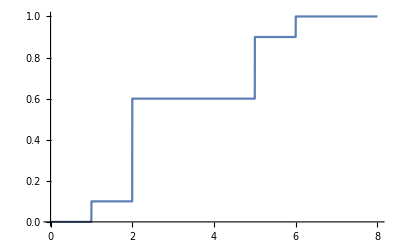

```mathematica
Plot[F[X],{X,0,8}]
```

```mathematica
(*3)*)
```

```mathematica
P(1≤ξ<4)=F[4]-F[1]
```

Set::write: Tag Times in P (1≤{{1,2,5,6},{0.1,0.5,0.3,0.1}}<4) is Protected.

0.6

```mathematica
(*4)*)
Media=∑_(j=1)^4 ξ[[1,j]]ξ[[2,j]]
```

3.2

```mathematica
(*5)*)
Dispersia=∑_(j=1)^4 (ξ[[1,j]]-Media)^2×ξ[[2,j]]
```

2.96

```mathematica
(*6)*)
abatere=√Dispersia
```

1.72047

```mathematica
(*7*)
a1=∑_(j=1)^4 (ξ[[1,j]])^1×ξ[[2,j]]
```

3.2

```mathematica
a2=∑_(j=1)^4 (ξ[[1,j]])^2×ξ[[2,j]]
```

13.2

```mathematica
a3=∑_(j=1)^4 (ξ[[1,j]])^3×ξ[[2,j]]
```

```mathematica
63.2
a4=∑_(j=1)^4 (ξ[[1,j]])^4×ξ[[2,j]]
```

325.2

```mathematica
(*8)*)
```

```mathematica
b1=∑_(j=1)^4 (ξ[[1,j]]-Media)^1×ξ[[2,j]]
```

-1.66533×10^-16

```mathematica
b2=∑_(j=1)^4 (ξ[[1,j]]-Media)^2×ξ[[2,j]]
```

2.96

```mathematica
b3=∑_(j=1)^4 (ξ[[1,j]]-Media)^3×ξ[[2,j]]
```

2.016

```mathematica
b4=∑_(j=1)^4 (ξ[[1,j]]-Media)^4×ξ[[2,j]]
```

12.6752

```mathematica
(*9)*)
```

```mathematica
Asimetria=b3/(abatere)^3
```

0.39587

```mathematica
(*10)*)
Excesul=b4/(abatere)^4-3
```

-1.55332